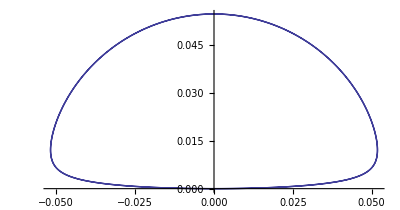

```mathematica
PolarPlot[Nest[Sin,θ,1000],{θ,0,2Pi}]
```

```mathematica
f[θ_]:=Nest[Sin,θ,1000]
ParametricPlot3D[{{f[θ]Cos[θ]Cos[ϕ],f[θ]Cos[θ]Sin[ϕ],f[θ]Sin[θ]}},{θ,0,π},{ϕ,0,2π}]
Export["c:/temp/bread.obj",%]
```

-Graphics3D-

c:/temp/bread.obj

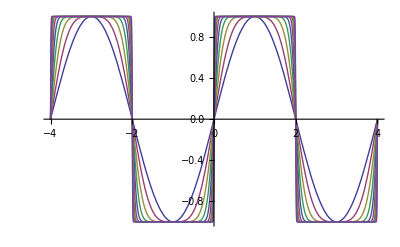

```mathematica
f[0]=x;
f[n_]:=Sin[Pi/2*f[n-1]];
Table[f[i],{i,1,10}];
Plot[%,{x,-4,4}]
```

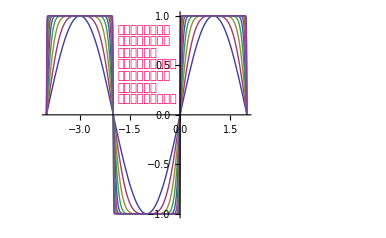

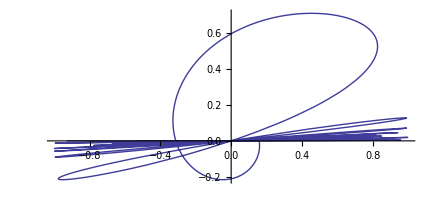

```mathematica
PolarPlot[Sin[1/θ],{θ,0,2Pi}]
```

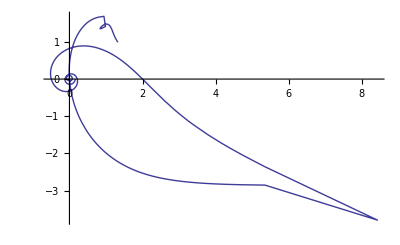

```mathematica
PolarPlot[Nest[Log,θ,3],{θ,0,8Pi}]
```

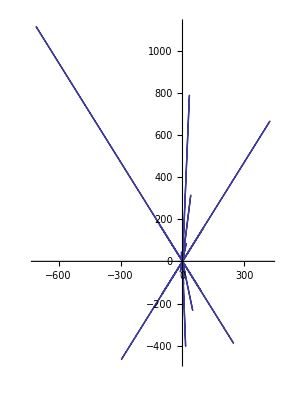

```mathematica
PolarPlot[Nest[Tan,θ,2],{θ,0,2Pi}]
```

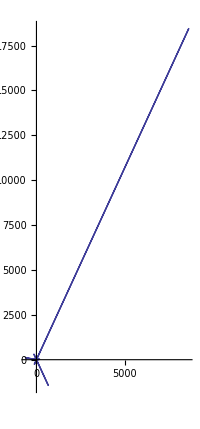

```mathematica
PolarPlot[Nest[Tan,θ/2,2],{θ,0,2Pi}]
```

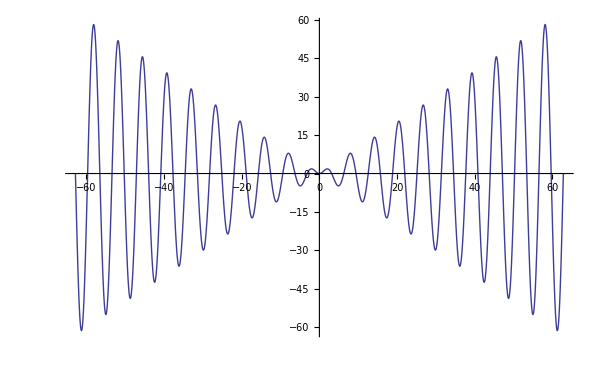

```mathematica
Plot[{Sin[x]  x},{x,-20Pi,20Pi}]
```

```mathematica
Manipulate[PolarPlot[Sqrt[b^2-(a Sin[θ]+ Sqrt[c^2-a^2  Cos[θ]^2])^2],{θ,-2Pi,2Pi}],{a,-10,10},{b,1,10},{c,1,10}]
```